# Diversity at the United World Colleges

The United World Colleges (UWC) are a group of currently 17 schools and National committees in 154 countries all around the world providing these high schools with the majority of their students. Initially founded in 1962 in Wales by German pedagogue Kurt Hahn, UWC aims to “make education a force to unite people, nations and cultures for peace and a sustainable future” (UWC Mission Statement). UWC tries to achieve this through several means, one important one being the diversity of the movement. In the following exploration, I will attempt to illustrate and measure diversity of UWC.

## Locations of UWC Schools

UWC aims to spread their schools as much across the globe as possible. To explore these locations, I created a dataset of UWCs and several interesting  parameters about them.

Import the dataset of UWC schools

```mathematica
schoolData=SortBy[SemanticImport["C:\\Users\\rbc15\\Desktop\\Mathematica\\WSS2018\\ComputationalEssay\SchoolData.csv"],"UWC since"]
```

Dataset[<>]

The first thing I want to do with this data is making the data easier to read. Below, for example, the Bar Chart makes it a lot easier to see how different in scale UWC South East Asia is to all the other UWC, because they serve a large number of local Singaporean students especially in the lower years.

Make a Chart showing the number of students attending each UWC

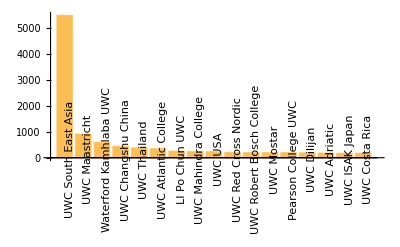

```mathematica
BarChart[ReverseSort[Map[Labeled[#[[2]],Rotate[#[[1]],Pi/2]]&,Normal[schoolData[All,{1,5}]]]]]
```

Another interesting plot to make is the geographical locations of different UWC schools around the world. The graph below shows, that there is a large concentration of UWC schools in Europe . Most other UWCs are more separated, with significant gaps in Africa, Central Eurasia and South America.

Make a plot of UWC schools’ locations.

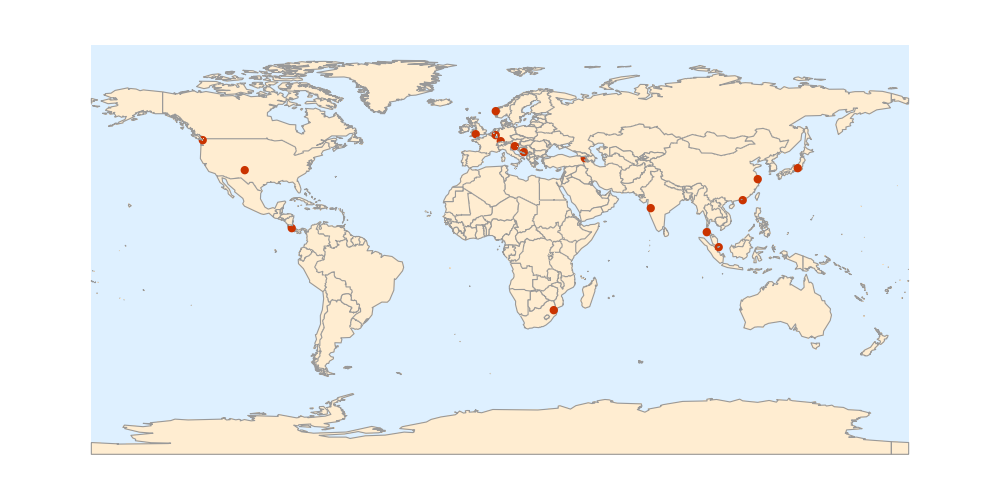

```mathematica
GeoListPlot[EntityValue[{Entity["AdministrativeDivision",{"ValeOfGlamorganThe","Wales","UnitedKingdom"}],Entity["City",{"Freiburg","BadenWurttemberg","Germany"}],Entity["City",{"SantaAna","SanJose","CostaRica"}],Entity["City",{"Pune","Maharashtra","India"}],Entity["City",{"Flekke","SognOgFjordane","Norway"}],Entity["City",{"Maastricht","Limburg","Netherlands"}] ,Entity["City",{"Karuizawa","Nagano","Japan"}],Entity["City",{"Singapore","Singapore","Singapore"}],Entity["AdministrativeDivision",{"DuinoAurisina","Trieste","FriuliVeneziaGiulia","Italy"}],Entity["City",{"Mostar","FederacijaBosnaIHercegovina","BosniaHerzegovina"}],Entity["City",{"HongKong","HongKong","HongKong"}], Entity["City",{"LasVegas","NewMexico","UnitedStates"}], Entity["City",{"Phuket","Phuket","Thailand"}], Entity["City",{"Mbabane","Hhohho","Swaziland"}],Entity["City",{"Victoria","BritishColumbia","Canada"}], Entity["City",{"Dilijan","Tavush","Armenia"}],Entity["City",{"Changshu","Jiangsu","China"}]},"Position"],GeoBackground->"CountryBorders",ImageSize->1000]
```

## Student Origin

Some of the UWC schools serve students for more than the two years of the International Baccalaureate Diploma Programme (IBDP), but those two years are the most essential, since they are the students selected by National Committees, most fulfilling the mission of UWC. I contacted the International Office of UWC and they were able to provide me with a dataset about the students attending UWC from different National Committees in the last three years.

Import the dataset on Students from different National Committees.

```mathematica
studentData = SemanticImport["C:\\Users\\rbc15\\Desktop\\Mathematica\\WSS2018\\Summer2018Starter\\ComputationalEssay\\IBDP students by country (3) .csv"]
```

Dataset[<>]

```mathematica
allcountries= EntityList[EntityClass["Country","Countries"]];
```

```mathematica
studentCountries=studentData[[All,3]]//DeleteDuplicates//Normal;
```

```mathematica
Thread[Complement[allcountries,studentCountries]->0];
```

```mathematica
Thread[Complement[EntityList[EntityClass["Country","Countries"]],studentData[[All,3]]//DeleteDuplicates//Normal]->0]
```

{Aland Islands→0,Algeria→0,American Samoa→0,Andorra→0,Anguilla→0,Antigua and Barbuda→0,Aruba→0,Azerbaijan→0,Caribbean Netherlands→0,Bouvet Island→0,British Indian Ocean Territory→0,British Virgin Islands→0,Brunei→0,Cape Verde→0,Central African Republic→0,Chad→0,Christmas Island→0,Cocos Keeling Islands→0,Comoros→0,Cook Islands→0,Curacao→0,Cyprus→0,Djibouti→0,Dominica→0,Equatorial Guinea→0,Eritrea→0,Falkland Islands→0,French Guiana→0,French Polynesia→0,French Southern And Antarctic lands→0,Gabon→0,Gambia→0,Gibraltar→0,Grenada→0,Guadeloupe→0,Guam→0,Guernsey→0,Guinea→0,Guinea-Bissau→0,Isle of Man→0,Jersey→0,Kiribati→0,Kyrgyzstan→0,Liechtenstein→0,Macau→0,Mali→0,Martinique→0,Mauritania→0,Mayotte→0,Micronesia→0,Monaco→0,Montserrat→0,Nauru→0,New Caledonia→0,Niger→0,Niue→0,Norfolk Island→0,Northern Mariana Islands→0,North Korea→0,Palau→0,Papua New Guinea→0,Pitcairn Islands→0,Puerto Rico→0,Qatar→0,Réunion→0,Saint Barthelemy→0,Saint Helena, Ascension and Tristan da Cunha→0,Saint Kitts and Nevis→0,Saint Lucia→0,Saint Martin→0,Saint Pierre and Miquelon→0,Saint Vincent and the Grenadines→0,Samoa→0,San Marino→0,São Tomé and Príncipe→0,Saudi Arabia→0,Seychelles→0,Sint Maarten→0,Solomon Islands→0,South Georgia and the South Sandwich Islands→0,Suriname→0,Svalbard→0,Taiwan→0,Togo→0,Tokelau→0,Tonga→0,Turkmenistan→0,Turks and Caicos Islands→0,Tuvalu→0,United States Minor Outlying Islands→0,United States Virgin Islands→0,Vatican City→0,Wallis and Futuna Islands→0,West Bank→0,Western Sahara→0}

One interesting thing to do with this data is looking at the coverage of the national committees. As seen in the map below, UWC selects students from almost every country, gaps exist only in the Sahara region (which already has low population density) and in other countries like North Korea. Some of these have small population numbers, randomizing the question whether there is a UWC student from the given country, others have political issues that may misalign them with UWC’s values.

Make a map of countries from which students attend UWC

```mathematica
GeoListPlot[DeleteDuplicates[studentData[All,3]],ImageSize->1000]
```

-Graphics-

However, the map above does not tell us enough about the actual diversity of the UWC students yet. There could be one student from each country, except for Madagascar, which provides all the other students. We could not tell from the graph. 
Below there is a graph, where the total number of students from a country attending UWC in the three years available to me determines the color the country is marked with. China is completely white due to the large number of students attending from there, we see some orange and red in India, Europe and North America, and large darker areas in South America, showing a relatively small number of students from those countries.

Make a map that shows countries with different numbers of students in different darkness levels

```mathematica
reds[x_]:=Blend[{White,Red,Black},x]
```

```mathematica
GeoRegionValuePlot[GroupBy[studentData[All,{3,5}],Lookup["Country (groups)"]->Last,Total],PlotStyle->EdgeForm[Thin],ImageSize->1000,GeoBackground->"CountryBorders",ColorFunction->(reds[#
]&)]
```

-Graphics-

```mathematica
Join[Thread[Complement[EntityList[EntityClass["Country","Countries"]],studentData[[All,3]]//DeleteDuplicates//Normal]->0]//Association,GroupBy[studentData[All,{3,5}],Lookup["Country (groups)"]->Last,Total]]
```

<|Aland Islands→0,Algeria→0,American Samoa→0,Andorra→0,Anguilla→0,Antigua and Barbuda→0,Aruba→0,Azerbaijan→0,Caribbean Netherlands→0,Bouvet Island→0,British Indian Ocean Territory→0,British Virgin Islands→0,Brunei→0,Cape Verde→0,Central African Republic→0,Chad→0,Christmas Island→0,Cocos Keeling Islands→0,Comoros→0,Cook Islands→0,Curacao→0,Cyprus→0,Djibouti→0,Dominica→0,Equatorial Guinea→0,Eritrea→0,Falkland Islands→0,French Guiana→0,French Polynesia→0,French Southern And Antarctic lands→0,Gabon→0,Gambia→0,Gibraltar→0,Grenada→0,Guadeloupe→0,Guam→0,Guernsey→0,Guinea→0,Guinea-Bissau→0,Isle of Man→0,Jersey→0,Kiribati→0,Kyrgyzstan→0,Liechtenstein→0,Macau→0,Mali→0,Martinique→0,Mauritania→0,Mayotte→0,Micronesia→0,Monaco→0,Montserrat→0,Nauru→0,New Caledonia→0,Niger→0,Niue→0,Norfolk Island→0,Northern Mariana Islands→0,North Korea→0,Palau→0,Papua New Guinea→0,Pitcairn Islands→0,Puerto Rico→0,Qatar→0,Réunion→0,Saint Barthelemy→0,Saint Helena, Ascension and Tristan da Cunha→0,Saint Kitts and Nevis→0,Saint Lucia→0,Saint Martin→0,Saint Pierre and Miquelon→0,Saint Vincent and the Grenadines→0,Samoa→0,San Marino→0,São Tomé and Príncipe→0,Saudi Arabia→0,Seychelles→0,Sint Maarten→0,Solomon Islands→0,South Georgia and the South Sandwich Islands→0,Suriname→0,Svalbard→0,Taiwan→0,Togo→0,Tokelau→0,Tonga→0,Turkmenistan→0,Turks and Caicos Islands→0,Tuvalu→0,United States Minor Outlying Islands→0,United States Virgin Islands→0,Vatican City→0,Wallis and Futuna Islands→0,West Bank→0,Western Sahara→0,Australia→15,Hong Kong→239,Japan→72,South Korea→15,New Zealand→11,Singapore→15,Austria→23,Belgium→32,Czech Republic→19,Denmark→74,Estonia→10,Faroe Islands→3,Finland→42,France→39,Germany→157,Greece→22,Greenland→9,Hungary→19,Iceland→1,Ireland→8,Italy→139,Latvia→7,Lithuania→7,Luxembourg→7,Netherlands→80,Norway→123,Poland→25,Portugal→43,Slovakia→16,Slovenia→13,Spain→53,Sweden→39,Switzerland→16,United Kingdom→157,Bahamas→10,Barbados→28,Cayman Islands→7,Chile→21,Trinidad and Tobago→11,Uruguay→8,Bahrain→10,Israel→54,Kuwait→1,Malta→6,Oman→21,United Arab Emirates→6,Bermuda→8,Canada→131,United States→172,Haiti→1,Afghanistan→29,Nepal→51,Benin→2,Burkina Faso→13,Burundi→4,Democratic Republic of the Congo→1,Ethiopia→21,Liberia→6,Madagascar→4,Malawi→8,Mozambique→7,Rwanda→13,Senegal→25,Sierra Leone→12,Somalia→12,South Sudan→18,Tanzania→12,Uganda→26,Zimbabwe→30,Cambodia→17,Indonesia→29,Laos→12,Mongolia→5,Myanmar→16,Philippines→20,East Timor→7,Vanuatu→1,Vietnam→30,Armenia→60,Georgia→23,Kosovo→11,Moldova→8,Tajikistan→5,Ukraine→21,Uzbekistan→1,Bolivia→12,El Salvador→29,Guatemala→18,Honduras→7,Nicaragua→8,Egypt→21,Jordan→20,Morocco→29,Syria→41,Tunisia→2,Gaza Strip→30,Yemen→5,Bangladesh→67,Bhutan→16,India→183,Pakistan→54,Sri Lanka→6,Angola→12,Cameroon→8,Republic of the Congo→3,Ivory Coast→6,Ghana→20,Kenya→31,Lesotho→15,Nigeria→97,Sudan→15,Swaziland→45,Zambia→7,China→381,Fiji→2,Malaysia→41,Marshall Islands→7,Thailand→25,Albania→20,Belarus→19,Bosnia and Herzegovina→100,Bulgaria→23,Croatia→12,Kazakhstan→13,Macedonia→10,Montenegro→14,Romania→12,Russia→52,Serbia→22,Turkey→42,Argentina→25,Belize→4,Brazil→27,Colombia→34,Costa Rica→49,Cuba→2,Dominican Republic→8,Ecuador→10,Guyana→12,Jamaica→15,Mexico→61,Panama→5,Paraguay→10,Peru→13,Venezuela→26,Iran→19,Iraq→22,Lebanon→44,Libya→4,Maldives→7,Botswana→10,Mauritius→20,Namibia→10,South Africa→24|>

If we make the assumption that UWC is trying to create a micro-society that is representative of the wider world. So let’s see what happens to the graph above, when we adjust the number for the population size of the country?
Now the front-runners are completely different. Greenland has the highest per capita concentration for students and other countries  in Scandinavia, Southern Africa or the former Balkan region have also become much lighter. China and India, our former front-runners are much darker, as many countries in South East Asia with large populations. Another important thing to not is that countries that did not send any students to a UWC are not marked in the plot even thought  they are of course underrepresented.
To make the data more visible I had to change the scale of the graph to a logarithmic one, making each color a multiple of the previous. The graph therefore under-represents the size of the differences between the countries.

```mathematica
GeoRegionValuePlot[Association[KeyValueMap[#1->Divide[#2,#1["Population"]//QuantityMagnitude//N]&,GroupBy[Normal[studentData[All,{3,5}]],Lookup["Country (groups)"]->Last,Total]]],ScalingFunctions->"Log2",ImageSize->1000,GeoBackground-> "CountryBorders",ColorFunction->reds]
```

-Graphics-

```mathematica
GroupBy[studentData
```